# Solving EOMs in Heisenberg picture

```mathematica
sx = PauliMatrix[1];sy = PauliMatrix[2];sz = PauliMatrix[3];id2=PauliMatrix[0];
comm[a_,b_]:=a.b-b.a;
heisEOM[H_,A_]:=ⅈ comm[H, A]
formVec[stringState_]:=Module[{up, down, right, left, mapping, vecList,vec},
up = {1, 0};
down = {0, 1};
right = {1, 1}/Sqrt[2];
left = {1, -1}/Sqrt[2];
mapping = <|"u"->up,"d"->down,"r"->right,"l"->left |>;
vecList =Lookup[Characters[stringState]]@mapping;
vec = KroneckerProduct@@vecList//Flatten;

Return[vec];
]
```

#### Beginning with H = ω σ_x and computing Z(t)

```mathematica
Clear[H, Z]
```

```mathematica
H = ω sx;
Z[t_]:=Table[Subscript[z, i,j][t], {i, 1, 2}, {j, 1, 2}]
Z'[t]
```

{{z_(1,1)'[t],z_(1,2)'[t]},{z_(2,1)'[t],z_(2,2)'[t]}}

```mathematica
DSolve[{Flatten[Z'[t]-heisEOM[H, Z[t]]]==ConstantArray[0, 4], Z[0]==sz}, Flatten[Z[t]], t]//FullSimplify
```

{{z_(1,1)[t]→Cos[2 t ω],z_(1,2)[t]→-ⅈ Sin[2 t ω],z_(2,1)[t]→ⅈ Sin[2 t ω],z_(2,2)[t]→-Cos[2 t ω]}}

#### Next H = ω_x σ_x+ω_y σ_y+ω_z σ_z and we compute Z(t)

```mathematica
Clear[H, Z]
```

```mathematica
H = Subscript[ω, x] sx + Subscript[ω, y] sy + Subscript[ω, z] sz;
Z[t_]:=Table[Subscript[z, i,j][t], {i, 1, 2}, {j, 1, 2}]
```

```mathematica
Eigenvalues[H]
```

{-√(ω_x^2+ω_y^2+ω_z^2),√(ω_x^2+ω_y^2+ω_z^2)}

```mathematica
DSolve[{Flatten[Z'[t]-heisEOM[H, Z[t]]]==ConstantArray[0, 4], Z[0]==sz}, Flatten[Z[t]], t]//FullSimplify
```

{{z_(1,1)[t]→(Cos[2 t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2)+ω_z^2)/(ω_x^2+ω_y^2+ω_z^2),z_(1,2)[t]→-(2 ⅈ Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x-ⅈ ω_y) (ⅈ Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_z √(ω_x^2+ω_y^2+ω_z^2)+Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2+ω_z^2)))/((ω_x^2+ω_y^2+ω_z^2)^(3/2)),z_(2,1)[t]→(2 ⅈ Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x+ⅈ ω_y) (-ⅈ Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_z √(ω_x^2+ω_y^2+ω_z^2)+Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2+ω_z^2)))/((ω_x^2+ω_y^2+ω_z^2)^(3/2)),z_(2,2)[t]→-(Cos[2 t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2)+ω_z^2)/(ω_x^2+ω_y^2+ω_z^2)}}

```mathematica
Clear[ut, matExpZ]
ut = MatrixExp[-ⅈ t H];
matExpZ = ConjugateTranspose[ut].sz.ut;
matExpZ//MatrixForm
```

(-Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2)))+Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))) | Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2)))-Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))
-Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2)))+Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))) | Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2)))-Conjugate[-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))] (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))))

```mathematica
FullSimplify[matExpZ, {t > 0, ωx∈Reals, ωy∈Reals, ωz∈Reals}]
```

$Aborted

```mathematica
Clear[ut, udgt, matExpZ]
```

```mathematica
ut = MatrixExp[-ⅈ t H];
udgt = Transpose[ComplexExpand[Conjugate[ut]]];
matExpZ = udgt.sz.ut;
matExpZ//MatrixForm
```

((-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))) (-(-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))-(1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+ⅈ ((-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))))+(-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))) (-(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))-ⅈ ((Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))) | (-(-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))-(1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+ⅈ ((-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2)))) (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))+(-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))) (-(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))-ⅈ ((Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))))
((-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))-ⅈ ((-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2)))) (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))+(-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x-ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))) ((Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))-(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+ⅈ ((Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))) | (-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (-ω_x+ⅈ ω_y))/(2 √(ω_x^2+ω_y^2+ω_z^2))) ((-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))-ⅈ ((-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x-1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))+(-1/2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)] ω_x+1/2 Cos[t √(ω_x^2+ω_y^2+ω_z^2)] ω_y)/(√(ω_x^2+ω_y^2+ω_z^2))))+(-(ⅇ^(-ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(ⅇ^(ⅈ t √(ω_x^2+ω_y^2+ω_z^2)) (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))) ((Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))-(Cos[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+ⅈ ((Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z-√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2))+(Sin[t √(ω_x^2+ω_y^2+ω_z^2)] (ω_z+√(ω_x^2+ω_y^2+ω_z^2)))/(2 √(ω_x^2+ω_y^2+ω_z^2)))))

```mathematica
FullSimplify[matExpZ, {t > 0, ωx∈Reals, ωy∈Reals, ωz∈Reals}]
```

{{(Cos[2 t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2)+ω_z^2)/(ω_x^2+ω_y^2+ω_z^2),((ω_x-ⅈ ω_y) (2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)]^2 ω_z-ⅈ Sin[2 t √(ω_x^2+ω_y^2+ω_z^2)] √(ω_x^2+ω_y^2+ω_z^2)))/(ω_x^2+ω_y^2+ω_z^2)},{((ω_x+ⅈ ω_y) (2 Sin[t √(ω_x^2+ω_y^2+ω_z^2)]^2 ω_z+ⅈ Sin[2 t √(ω_x^2+ω_y^2+ω_z^2)] √(ω_x^2+ω_y^2+ω_z^2)))/(ω_x^2+ω_y^2+ω_z^2),-(Cos[2 t √(ω_x^2+ω_y^2+ω_z^2)] (ω_x^2+ω_y^2)+ω_z^2)/(ω_x^2+ω_y^2+ω_z^2)}}

#### Try H = -Γ (X1 + X2 + X3) (actually solves fast enough to have generic Γ and use DSolve

```mathematica
Clear[H, Z1, Z2, Z3, z1Sol, z2Sol, z3Sol]
```

```mathematica
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
H =-Γ(sx1 + sx2 + sx3);
Z1[t_]:=Table[Subscript[z1, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z2[t_]:=Table[Subscript[z2, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z3[t_]:=Table[Subscript[z3, i,j][t], {i, 1, 8}, {j, 1, 8}];
```

```mathematica
z1Sol = DSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]]==ConstantArray[0, 64],Z1[0]==sz1}, Flatten[Z1[t]], t]//FullSimplify;
z2Sol = DSolve[{Flatten[Z2'[t]-heisEOM[H, Z2[t]]]==ConstantArray[0, 64],Z2[0]==sz2}, Flatten[Z2[t]], t]//FullSimplify;
z3Sol = DSolve[{Flatten[Z3'[t]-heisEOM[H, Z3[t]]]==ConstantArray[0, 64],Z3[0]==sz3}, Flatten[Z3[t]], t]//FullSimplify;
```

```mathematica
z1Sol
```

{{z1_(1,1)[t]→Cos[2 t Γ],z1_(1,2)[t]→0,z1_(1,3)[t]→0,z1_(1,4)[t]→0,z1_(1,5)[t]→ⅈ Sin[2 t Γ],z1_(1,6)[t]→0,z1_(1,7)[t]→0,z1_(1,8)[t]→0,z1_(2,1)[t]→0,z1_(2,2)[t]→Cos[2 t Γ],z1_(2,3)[t]→0,z1_(2,4)[t]→0,z1_(2,5)[t]→0,z1_(2,6)[t]→ⅈ Sin[2 t Γ],z1_(2,7)[t]→0,z1_(2,8)[t]→0,z1_(3,1)[t]→0,z1_(3,2)[t]→0,z1_(3,3)[t]→Cos[2 t Γ],z1_(3,4)[t]→0,z1_(3,5)[t]→0,z1_(3,6)[t]→0,z1_(3,7)[t]→ⅈ Sin[2 t Γ],z1_(3,8)[t]→0,z1_(4,1)[t]→0,z1_(4,2)[t]→0,z1_(4,3)[t]→0,z1_(4,4)[t]→Cos[2 t Γ],z1_(4,5)[t]→0,z1_(4,6)[t]→0,z1_(4,7)[t]→0,z1_(4,8)[t]→ⅈ Sin[2 t Γ],z1_(5,1)[t]→-ⅈ Sin[2 t Γ],z1_(5,2)[t]→0,z1_(5,3)[t]→0,z1_(5,4)[t]→0,z1_(5,5)[t]→-Cos[2 t Γ],z1_(5,6)[t]→0,z1_(5,7)[t]→0,z1_(5,8)[t]→0,z1_(6,1)[t]→0,z1_(6,2)[t]→-ⅈ Sin[2 t Γ],z1_(6,3)[t]→0,z1_(6,4)[t]→0,z1_(6,5)[t]→0,z1_(6,6)[t]→-Cos[2 t Γ],z1_(6,7)[t]→0,z1_(6,8)[t]→0,z1_(7,1)[t]→0,z1_(7,2)[t]→0,z1_(7,3)[t]→-ⅈ Sin[2 t Γ],z1_(7,4)[t]→0,z1_(7,5)[t]→0,z1_(7,6)[t]→0,z1_(7,7)[t]→-Cos[2 t Γ],z1_(7,8)[t]→0,z1_(8,1)[t]→0,z1_(8,2)[t]→0,z1_(8,3)[t]→0,z1_(8,4)[t]→-ⅈ Sin[2 t Γ],z1_(8,5)[t]→0,z1_(8,6)[t]→0,z1_(8,7)[t]→0,z1_(8,8)[t]→-Cos[2 t Γ]}}

```mathematica
udgt = MatrixExp[ⅈ H t];
```

```mathematica
altZ1Sol = FullSimplify[udgt.sz1.ConjugateTranspose[udgt], {t>0,Γ>0}]
```

{{Cos[2 t Γ],0,0,0,ⅈ Sin[2 t Γ],0,0,0},{0,Cos[2 t Γ],0,0,0,ⅈ Sin[2 t Γ],0,0},{0,0,Cos[2 t Γ],0,0,0,ⅈ Sin[2 t Γ],0},{0,0,0,Cos[2 t Γ],0,0,0,ⅈ Sin[2 t Γ]},{-ⅈ Sin[2 t Γ],0,0,0,-Cos[2 t Γ],0,0,0},{0,-ⅈ Sin[2 t Γ],0,0,0,-Cos[2 t Γ],0,0},{0,0,-ⅈ Sin[2 t Γ],0,0,0,-Cos[2 t Γ],0},{0,0,0,-ⅈ Sin[2 t Γ],0,0,0,-Cos[2 t Γ]}}

#### Try H = -0.1 (X1 + X2 + X3) + (Z1Z2 + Z1Z3 + Z2Z3) (also took very long time, so better to solve with NDSolve)

```mathematica
Clear[H, Z1, Z2, Z3, z1Sol, z2Sol, z3Sol, matExpZ1Sol, udgt]
```

```mathematica
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
H =-0.1(sx1 + sx2 + sx3) + (sz1.sz2+sz1.sz3+sz2.sz3);
Z1[t_]:=Table[Subscript[z1, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z2[t_]:=Table[Subscript[z2, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z3[t_]:=Table[Subscript[z3, i,j][t], {i, 1, 8}, {j, 1, 8}];
```

```mathematica
Clear[ut, udgt, matExpZ1]
ut = MatrixExp[-ⅈ t H];
udgt = Transpose[ComplexExpand[Conjugate[ut]]];
matExpZ1 = udgt.sz1.ut;
```

```mathematica
Simplify[matExpZ1, {t > 0}]
```

```mathematica
z1Sol=NDSolve[{Flatten[Z1'[t]-heisEOM[H,Z1[t]]]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

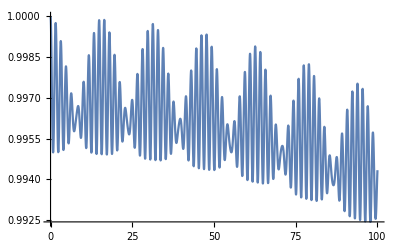

```mathematica
Plot[z1Sol[[1,1]][[2]], {t, 0, 100}]
```

```mathematica
z2Sol=NDSolve[{Flatten[Z2'[t]-heisEOM[H,Z2[t]]]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],t];
z3Sol=NDSolve[{Flatten[Z3'[t]-heisEOM[H,Z3[t]]]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],t];
```

#### Try H = -0.1 (X1 + X2 + X3) + (Z1Z2 + Z1Z3 + Z2Z3) with pre-processing tricks on commutator

```mathematica
Clear[H, Z1, Z2, Z3, z1Sol, z2Sol, z3Sol]
```

```mathematica
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
H =-0.1(sx1 + sx2 + sx3) + (sz1.sz2+sz1.sz3+sz2.sz3);
Z1[t_]:=Table[Subscript[z1, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z2[t_]:=Table[Subscript[z2, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z3[t_]:=Table[Subscript[z3, i,j][t], {i, 1, 8}, {j, 1, 8}];
```

```mathematica
z1Sol=NDSolve[{Flatten[Z1'[t]-heisEOM[H,Z1[t]]]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

```mathematica
Plot[z1Sol[[1,1]][[2]], {t, 0, 100}]
```

-Graphics-

```mathematica
z2Sol=NDSolve[{Flatten[Z2'[t]-heisEOM[H,Z2[t]]]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],t];
z3Sol=NDSolve[{Flatten[Z3'[t]-heisEOM[H,Z3[t]]]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],t];
```

```mathematica
comm[sx, sz]
```

{{0,-2},{2,0}}

```mathematica
-2 ⅈ sy
```

{{0,-2},{2,0}}

```mathematica
comm[sy,sz]
```

{{0,2 ⅈ},{2 ⅈ,0}}

```mathematica
2ⅈ sx
```

{{0,2 ⅈ},{2 ⅈ,0}}

#### Try H = -Γ (X1 + X2 + X3) + J(Z1Z2 + Z1Z3 + Z2Z3) + h_1 Z1+ h_2 Z2+ h_3 Z3

```mathematica
Clear[H, Z1, Z2, Z3]
```

```mathematica
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
sy1 = KroneckerProduct[sy, id2, id2];sy2 = KroneckerProduct[id2, sy, id2];sy3 = KroneckerProduct[id2, id2, sy];
H =-Γ(sx1 + sx2 + sx3) + J(sz1.sz2+sz1.sz3+sz2.sz3) + h1 sz1 + h2 sz2 + h3 sz3;
Z1[t_]:=Table[Subscript[z1, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z2[t_]:=Table[Subscript[z2, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z3[t_]:=Table[Subscript[z3, i,j][t], {i, 1, 8}, {j, 1, 8}];
```

```mathematica
Clear[ut, udgt, matExpZ1]
ut = MatrixExp[-ⅈ t H];
udgt = Transpose[ComplexExpand[Conjugate[ut]]];
matExpZ1 = udgt.sz1.ut;
```

$Aborted

```mathematica
z1Sol=DSolve[{Flatten[Z1'[t]+2 Γ udgt.sy1.ut/.{Γ->0.1,J->1,h1->0,h2->0,h3->0}]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],t];
```

FactorSquareFree::lrgexp: Exponent is out of bounds for function FactorSquareFree.

General::stop: Further output of FactorSquareFree::lrgexp will be suppressed during this calculation.

```mathematica
N[z1Sol[[1, 1]]/.{t->0.1}];
```

```mathematica
z1Sol=DSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]/.{Γ->0.1,J->1,h1->0,h2->0,h3->0}]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],t];
```

$Aborted

```mathematica
z1Sol=NDSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]/.{Γ->0.1,J->1,h1->0,h2->0,h3->0}]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

```mathematica
phi0 = formVec["uud"];
```

```mathematica
2 Γ udgt.sy1.ut/.{Γ->0.1,J->1,h1->0,h2->0,h3->0}
```

```mathematica
z1Sol=DSolve[{Flatten[Z1'[t]-heisEOM[H,Z1[t]]]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

$Aborted

```mathematica
z1Sol=DSolve[{Flatten[Z1'[t]-]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

```mathematica
z2Sol=NDSolve[{Flatten[Z2'[t]-heisEOM[H,Z2[t]]]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],t];
z3Sol=NDSolve[{Flatten[Z3'[t]-heisEOM[H,Z3[t]]]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],t];
```

```mathematica
z1Sol=DSolve[{Flatten[Z1'[t]-heisEOM[H,Z1[t]]]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, 100}];
```

```mathematica
(Z1'[t])[[1,2]]
```

z1_(1,2)'[t]

```mathematica
Clear[k, l, j]
k = 1; l = 1;
temp0 = (Z1'[t])[[k,l]];
temp1 = Sum[H[[k,j]]*Z1[t][[j, l]], {j, 1, 8}];
temp2 = Sum[Z1[t][[k, j]]*H[[j,l]],{j, 1, 8}];
DSolve[{temp0 -ⅈ(temp1-temp2)==0, Z1[0][[k,l]]==sz1[[k,l]]},Subscript[z1, k,l][t],t]
```

{{z1_(1,1)[t]→1+ⅈ (Γ z1_(1,2)[K[1]]+Γ z1_(1,3)[K[1]]+Γ z1_(1,5)[K[1]]-Γ z1_(2,1)[K[1]]-Γ z1_(3,1)[K[1]]-Γ z1_(5,1)[K[1]])K[1]0t}}

#### Try H = -Γ(X1 + X2 + X3) + J (Z1Z2 + Z1Z3 + Z2Z3) + 0Z1+ 0Z2+ 0Z3

```mathematica
Clear[H, Z1, Z2, Z3]
```

```mathematica
sx1 = KroneckerProduct[sx, id2, id2]; sx2 = KroneckerProduct[id2, sx, id2]; sx3 = KroneckerProduct[id2, id2, sx];
sz1 = KroneckerProduct[sz, id2, id2];sz2 = KroneckerProduct[id2, sz, id2];sz3 = KroneckerProduct[id2, id2, sz];
sy1 = KroneckerProduct[sy, id2, id2];sy2 = KroneckerProduct[id2, sy, id2];sy3 = KroneckerProduct[id2, id2, sy];
H =-Γ(sx1 + sx2 + sx3) + J(sz1.sz2+sz1.sz3+sz2.sz3) + h1 sz1 + h2 sz2 + h3 sz3z;
Z1[t_]:=Table[Subscript[z1, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z2[t_]:=Table[Subscript[z2, i,j][t], {i, 1, 8}, {j, 1, 8}];
Z3[t_]:=Table[Subscript[z3, i,j][t], {i, 1, 8}, {j, 1, 8}];
```

#### Solving with Γ = 0.1, J = 1, h_i = 0

```mathematica
params = {Γ->0.1,J->1,h1->0,h2->0,h3->0};
tf = 100;
z1Sol=First[Z1[t]/.NDSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]/.params]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, tf}]];
z2Sol=First[Z2[t]/.NDSolve[{Flatten[Z2'[t]-heisEOM[H, Z2[t]]/.params]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],{t, 0, tf}]];
z3Sol=First[Z3[t]/.NDSolve[{Flatten[Z3'[t]-heisEOM[H, Z3[t]]/.params]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],{t, 0, tf}]];
psiSol = z1Sol + z2Sol*Exp[ⅈ 2 π / 3] + z3Sol*Exp[ⅈ 4 π /3];
```

```mathematica
params2 = {Γ->0.1,J->1,h1->1,h2->0,h3->0};
tf = 100;
z1Solh1=First[Z1[t]/.NDSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]/.params2]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, tf}]];
z2Solh1=First[Z2[t]/.NDSolve[{Flatten[Z2'[t]-heisEOM[H, Z2[t]]/.params2]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],{t, 0, tf}]];
z3Solh1=First[Z3[t]/.NDSolve[{Flatten[Z3'[t]-heisEOM[H, Z3[t]]/.params2]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],{t, 0, tf}]];
psiSolh1 = z1Solh1 + z2Solh1*Exp[ⅈ 2 π / 3] + z3Solh1*Exp[ⅈ 4 π /3];
```

```mathematica
params2 = {Γ->0.1,J->1,h1->1,h2->1,h3->0};
tf = 100;
z1Solh1=First[Z1[t]/.NDSolve[{Flatten[Z1'[t]-heisEOM[H, Z1[t]]/.params2]==ConstantArray[0,64],Z1[0]==sz1},Flatten[Z1[t]],{t, 0, tf}]];
z2Solh1=First[Z2[t]/.NDSolve[{Flatten[Z2'[t]-heisEOM[H, Z2[t]]/.params2]==ConstantArray[0,64],Z2[0]==sz2},Flatten[Z2[t]],{t, 0, tf}]];
z3Solh1=First[Z3[t]/.NDSolve[{Flatten[Z3'[t]-heisEOM[H, Z3[t]]/.params2]==ConstantArray[0,64],Z3[0]==sz3},Flatten[Z3[t]],{t, 0, tf}]];
psiSolh1 = z1Solh1 + z2Solh1*Exp[ⅈ 2 π / 3] + z3Solh1*Exp[ⅈ 4 π /3];
```

#### Analysis of solution for “diagonal element,” i.e. applied to |up up down>

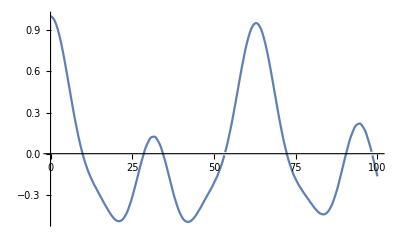

```mathematica
Plot[formVec["uud"].z1Sol.formVec["uud"], {t, 0, 100}]
```

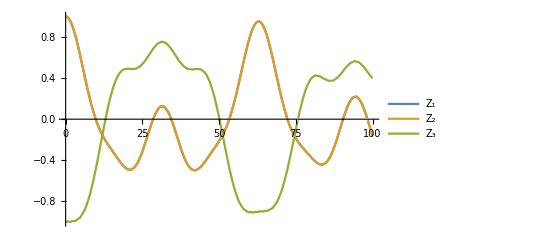

```mathematica
Plot[{z1Sol[[2,2]],z2Sol[[2,2]],z3Sol[[2,2]]}, {t, 0, 100}, PlotLegends->{"Z_1","Z_2","Z_3"}]
```

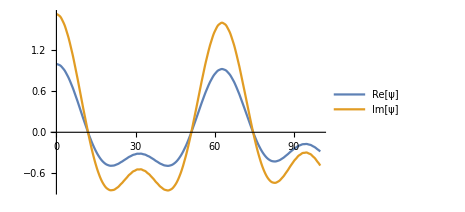
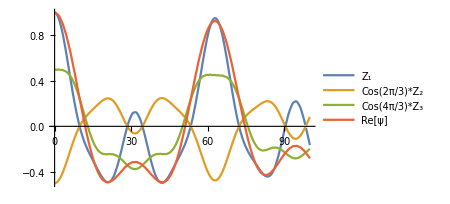
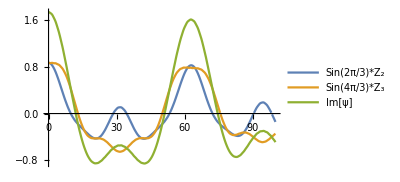

```mathematica
{Plot[{psiSol[[2,2]]//Re, psiSol[[2,2]]//Im}, {t, 0, 100}, PlotLegends->{"Re[ψ]","Im[ψ]"}], Plot[{z1Sol[[2,2]],Cos[2π/3]*z2Sol[[2,2]],Cos[4π/3]z3Sol[[2,2]],psiSol[[2,2]]//Re}, {t, 0, 100}, PlotLegends->{"Z_1","Cos(2π/3)*Z_2","Cos(4π/3)*Z_3", "Re[ψ]"}], Plot[{Sin[2π/3]*z2Sol[[2,2]],Sin[4π/3]z3Sol[[2,2]],psiSol[[2,2]]//Im}, {t, 0, 100}, PlotLegends->{"Sin(2π/3)*Z_2","Sin(4π/3)*Z_3", "Im[ψ]"}]}
```

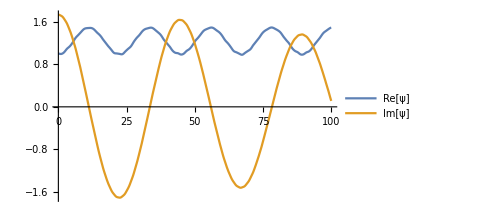
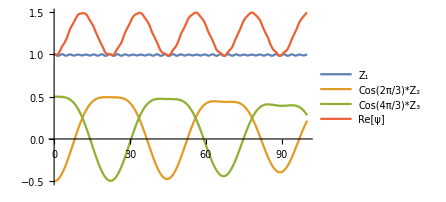
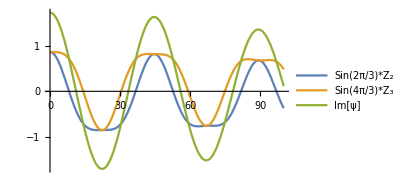

```mathematica
{Plot[{psiSolh1[[2,2]]//Re, psiSolh1[[2,2]]//Im}, {t, 0, 100}, PlotLegends->{"Re[ψ]","Im[ψ]"}], Plot[{z1Solh1[[2,2]],Cos[2π/3]*z2Solh1[[2,2]],Cos[4π/3]z3Solh1[[2,2]],psiSolh1[[2,2]]//Re}, {t, 0, 100}, PlotLegends->{"Z_1","Cos(2π/3)*Z_2","Cos(4π/3)*Z_3", "Re[ψ]"}], Plot[{Sin[2π/3]*z2Solh1[[2,2]],Sin[4π/3]z3Solh1[[2,2]],psiSolh1[[2,2]]//Im}, {t, 0, 100}, PlotLegends->{"Sin(2π/3)*Z_2","Sin(4π/3)*Z_3", "Im[ψ]"}]}
```

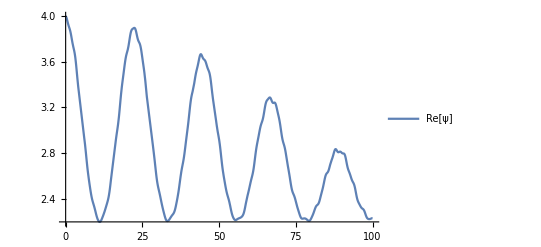

°[1]

```mathematica
Plot[{(psiSolh1[[2,2]]//Re)^2+( psiSolh1[[2,2]]//Im)^2}, {t, 0, 100}, PlotLegends->{"Re[ψ]","Im[ψ]"}]
```

```mathematica
Sort[Eigenvalues[H/.{params2}]]
```

{-2.14717,-2.00499,-1.86454,-0.143141,0.00498756,0.138155,2.01002,4.00667}

```mathematica
-2.004987562112089+2.1471660873083445
```

0.142179

```mathematica
∂
```

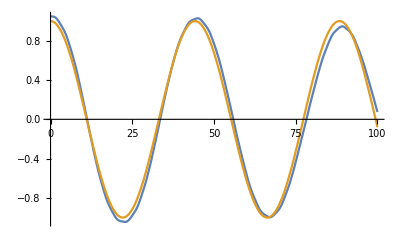

```mathematica
Plot[{ArcTan[Re[psiSolh1[[2,2]]],Im[psiSolh1[[2,2]]]], Cos[0.1421785251962553t]}, {t, 0, 100}]
```

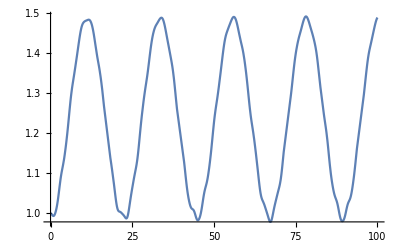

```mathematica
Plot[Re[psiSolh1[[2,2]]], {t, 0, 100}]
```

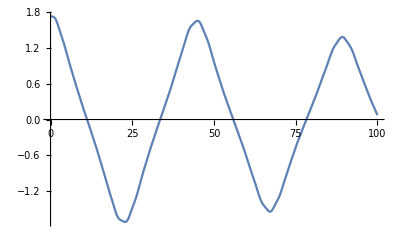

```mathematica
Plot[Im[psiSolh1[[2,2]]]/Re[psiSolh1[[2,2]]], {t, 0, 100}]
```

```mathematica
Plot[{(psiSolh1[[2,2]]//Re)^2+( psiSolh1[[2,2]]//Im)^2}, {t, 0, 100}, PlotLegends->{"Re[ψ]","Im[ψ]"}]
```

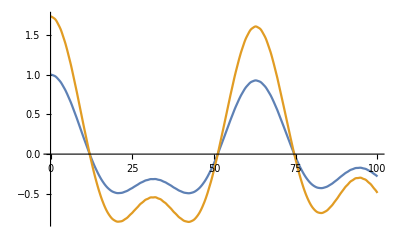

```mathematica
Plot[{psiSol[[2,2]]//Re, psiSol[[2,2]]//Im}, {t, 0, 100}]
```

```mathematica
Animate[ListPlot[{{pSpinPoints[[i]]}, {pSpinPointsp[[i]]}, {pSpinPointsm[[i]]}}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H", "H + Z_1", "H - Z_1"}], {i, 1, Length[pSpinPoints], 1}]
```

```mathematica
ut = MatrixExp[-ⅈ t H/.params2];
utdg = Transpose[ComplexExpand[Conjugate[ut]]];
```

```mathematica
realSol = (utdg.(sz1+Cos[2π/3]*sz2+Cos[4π/3]*sz3).ut)[[2,2]];
realSol = Chop[FullSimplify[Chop[realSol,10^-8]], 10^-8];
imagSol = (utdg.(Sin[2π/3]*sz2+Sin[4π/3]*sz3).ut)[[2,2]];
imagSol = Chop[FullSimplify[Chop[imagSol,10^-8]], 10^-8]
```

0.288079 ⅇ^((0.-0.0921216 ⅈ) t)+0.288079 ⅇ^((0.+0.0921216 ⅈ) t)+0.288187 ⅇ^((0.-0.107131 ⅈ) t)+0.288187 ⅇ^((0.+0.107131 ⅈ) t)+0.288675 ⅇ^((0.-0.2 ⅈ) t)+0.288675 ⅇ^((0.+0.2 ⅈ) t)+0.000596028 ⅇ^((0.-3.90788 ⅈ) t)+0.000596028 ⅇ^((0.+3.90788 ⅈ) t)+0.000488453 ⅇ^((0.-4.10713 ⅈ) t)+0.000488453 ⅇ^((0.+4.10713 ⅈ) t)

```mathematica
blah = Chop[FullSimplify[Chop[realSol,10^-8]], 10^-8]
```

0.332645 Cos[0.0921216 t]-0.188094 Cos[0.107131 t]+0.520863 Cos[0.107131 t]+0.330002 Cos[0.2 t]+0.00333178 Cos[0.2 t]+0.000688234 Cos[3.90788 t]+0.000882822 Cos[4.10713 t]-0.000318805 Cos[4.10713 t]+0.317802 Sin[0.107131 t]-0.317802 Sin[0.107131 t]-0.617419 Sin[0.2 t]+0.617419 Sin[0.2 t]+0.000538649 Sin[4.10713 t]-0.000538649 Sin[4.10713 t]

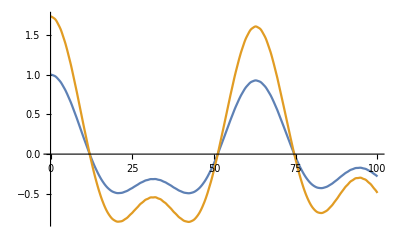

```mathematica
Plot[{realSol,imagSol//Re}, {t, 0, 100}]
```

```mathematica
points = Table[{realSol/.{t->tp},imagSol/.{t->tp}//Re}, {tp, 0, 100,1/10}];
```

```mathematica
Animate[ListPlot[{points[[i]]}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H"}], {i, 1, Length[points], 1}]
```

### Solving with Γ = 0.1, J = 1, h_1 = 1

```mathematica
params = {Γ->0.1,J->1,h1->1,h2->-1,h3->0};
ut = MatrixExp[-ⅈ t H/.params];
utdg = Transpose[ComplexExpand[Conjugate[ut]]];
sol = (utdg.(sz1+Exp[ⅈ 2π/3]*sz2+Exp[ⅈ 4π/3]*sz3).ut)[[2,2]];
points = Table[{Re[#],Im[#]}&@(sol/.{t->tp}), {tp, 0, tf,1/10}];
```

```mathematica
Animate[ListPlot[{points[[i]]}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H"}], {i, 1, Length[points], 1}]
```

```mathematica
params = {Γ->0.1,J->1,h1->1,h2->0,h3->0};
ut = MatrixExp[-ⅈ t H/.params];
utdg = Transpose[ComplexExpand[Conjugate[ut]]];
realSol = (utdg.(sz1+Cos[2π/3]*sz2+Cos[4π/3]*sz3).ut)[[2,2]];
realSol = Chop[FullSimplify[Chop[realSol,10^-8]], 10^-8];
imagSol = (utdg.(Sin[2π/3]*sz2+Sin[4π/3]*sz3).ut)[[2,2]];
imagSol = Chop[FullSimplify[Chop[imagSol,10^-8]], 10^-8]
points = Table[{realSol/.{t->tp},imagSol/.{t->tp}//Re}, {tp, 0, tf,1/10}];
```

```mathematica
Animate[ListPlot[{{Re[Exp[-ⅈ 2 t]], Im[Exp[-ⅈ 2 t]]}}, PlotRange->{{-3, 3}, {-3, 3}}, PlotMarkers->{Automatic, 12.5}, PlotLegends->{"H"}], {t, 0, 10}]
```

```mathematica
params = {Γ->0.1,J->1};
ut = MatrixExp[-ⅈ t H/.params];
```

```mathematica
choppedUt = Chop[ut]
```

```mathematica
choppedUt.formVec["uud"]
```

```mathematica
comm[{A_, B_}] := {A, A.B - B.A}
Rest[Nest[comm,{a,b},2]]
{a.(a.b-b.a)-(a.b-b.a).a}
```

## Doing commutator stuff a la Magnus type expansion

```mathematica
Clear[comm]
comm[{B_,A_}]:={B, B.A-A.B};
Rest[Nest[comm, {b, a}, 2]]
```

{b.(-a.b+b.a)-(-a.b+b.a).b}

```mathematica
Rest[Nest[comm, {H, sy1}, 1]]//First
```

{{2 ⅈ (h3 sz3z-Γ),2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z),0,0,0},{2 ⅈ h3 sz3z,2 ⅈ (h3 sz3z-Γ),2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,0,ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z),0,0},{2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,2 ⅈ (h3 sz3z-Γ),2 ⅈ h3 sz3z,0,0,ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z),0},{2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,2 ⅈ h3 sz3z,2 ⅈ (h3 sz3z-Γ),0,0,0,-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)},{ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z),0,0,0,-2 ⅈ (h3 sz3z-Γ),-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z},{0,ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z),0,0,-2 ⅈ h3 sz3z,-2 ⅈ (h3 sz3z-Γ),-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z},{0,0,ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z),0,-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z,-2 ⅈ (h3 sz3z-Γ),-2 ⅈ h3 sz3z},{0,0,0,-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z),-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z,-2 ⅈ h3 sz3z,-2 ⅈ (h3 sz3z-Γ)}}

```mathematica
Rest[Nest[comm, {H, sy1}, 2]]
```

{{{0,-2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)+2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),-2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),-2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),-12 ⅈ h3^2 sz3z^2-(-h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))+(h1+h2+3 J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))-4 ⅈ (h3 sz3z-Γ)^2,-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))-8 ⅈ h3 sz3z (h3 sz3z-Γ)},{2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)-2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),0,-2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)),-2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-12 ⅈ h3^2 sz3z^2-(-h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+(h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-4 ⅈ (h3 sz3z-Γ)^2,-8 ⅈ h3^2 sz3z^2+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-8 ⅈ h3 sz3z (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)+(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ)},{2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)),0,-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-8 ⅈ h3 sz3z (h3 sz3z-Γ),-12 ⅈ h3^2 sz3z^2-(-h1-h2-J+h3 sz3z) (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+(h1-h2-J+h3 sz3z) (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-4 ⅈ (h3 sz3z-Γ)^2,-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)+(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ)},{2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (h1+h2+3 J+h3 sz3z)-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),2 ⅈ h3 sz3z (h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (h1+h2-J+h3 sz3z)+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),0,-8 ⅈ h3^2 sz3z^2-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))-8 ⅈ h3 sz3z (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)-(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-8 ⅈ h3^2 sz3z^2-8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)-(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-12 ⅈ h3^2 sz3z^2+(h1-h2-J+h3 sz3z) (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-(-h1-h2+3 J+h3 sz3z) (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-4 ⅈ (h3 sz3z-Γ)^2},{12 ⅈ h3^2 sz3z^2+(-h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))-(h1+h2+3 J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))+4 ⅈ (h3 sz3z-Γ)^2,8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))+8 ⅈ h3 sz3z (h3 sz3z-Γ),0,h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),-2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)+2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))},{8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),12 ⅈ h3^2 sz3z^2+(-h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-(h1+h2-J+h3 sz3z) (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+4 ⅈ (h3 sz3z-Γ)^2,8 ⅈ h3^2 sz3z^2+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+8 ⅈ h3 sz3z (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)+(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),0,2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)),-2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)+2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)-h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))},{8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)) (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))+8 ⅈ h3 sz3z (h3 sz3z-Γ),12 ⅈ h3^2 sz3z^2+(-h1-h2-J+h3 sz3z) (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-(h1-h2-J+h3 sz3z) (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+4 ⅈ (h3 sz3z-Γ)^2,8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)-(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)+(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),-2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),-2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)),0,-2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)+2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)-h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))+h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))},{8 ⅈ h3^2 sz3z^2-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z))+8 ⅈ h3 sz3z (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z)) (h3 sz3z-Γ)-(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),8 ⅈ h3^2 sz3z^2+8 ⅈ h3 sz3z (h3 sz3z-Γ)+(ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z)) (h3 sz3z-Γ)-(-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)) (h3 sz3z-Γ),12 ⅈ h3^2 sz3z^2-(h1-h2-J+h3 sz3z) (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+(-h1-h2+3 J+h3 sz3z) (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+4 ⅈ (h3 sz3z-Γ)^2,2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)-2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z))+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2+3 J+h3 sz3z)),2 ⅈ h3 sz3z (-h1+h2-J+h3 sz3z)-2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)+h3 sz3z (ⅈ (-h1+h2-J+h3 sz3z)-ⅈ (h1+h2-J+h3 sz3z))-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),2 ⅈ h3 sz3z (-h1-h2-J+h3 sz3z)-2 ⅈ h3 sz3z (-h1-h2+3 J+h3 sz3z)+h3 sz3z (ⅈ (-h1-h2-J+h3 sz3z)-ⅈ (h1-h2-J+h3 sz3z))-h3 sz3z (-ⅈ (h1-h2-J+h3 sz3z)+ⅈ (-h1-h2+3 J+h3 sz3z)),0}}}

### Let’s just find the basis in which Hamiltonian is diagonal and then write operators in this basis

```mathematica
Clear[H, h]
```

```mathematica
H = ωx PauliMatrix[1] + ωy PauliMatrix[2] + ωz PauliMatrix[3];
```

```mathematica
λ = Eigenvalues[H]
```

{-√(ωx^2+ωy^2+ωz^2),√(ωx^2+ωy^2+ωz^2)}

```mathematica
v = Eigenvectors[H]
```

{{-(-ωz+√(ωx^2+ωy^2+ωz^2))/(ωx+ⅈ ωy),1},{-(-ωz-√(ωx^2+ωy^2+ωz^2))/(ωx+ⅈ ωy),1}}

```mathematica
c = Table[ComplexExpand[Conjugate[v[[i]]]].PauliMatrix[3].v[[j]], {i, 1, Length[v]}, {j, 1, Length[v]}]
```

{{-1-((-ωz+√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy),-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)},{-1-((-ωz+√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)+(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)+(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy),-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)+(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)+(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)}}

```mathematica
c[[1, 2]]
```

-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)

```mathematica
zt = Table[Exp[λ[[i]]]*Exp[ComplexExpand[Conjugate[λ[[j]]]]*c[[1,2]]], {i, 1, Length[λ]}, {j, 1, Length[λ]}]
```

{{ⅇ^(-√(ωx^2+ωy^2+ωz^2)-√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy))),ⅇ^(-√(ωx^2+ωy^2+ωz^2)+√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)))},{ⅇ^(√(ωx^2+ωy^2+ωz^2)-√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy))),ⅇ^(√(ωx^2+ωy^2+ωz^2)+√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)))}}

```mathematica
zt//MatrixForm
```

(ⅇ^(-√(ωx^2+ωy^2+ωz^2)-√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy))) | ⅇ^(-√(ωx^2+ωy^2+ωz^2)+√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy)))
ⅇ^(√(ωx^2+ωy^2+ωz^2)-√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy))) | ⅇ^(√(ωx^2+ωy^2+ωz^2)+√(ωx^2+ωy^2+ωz^2) (-1-((-ωz-√(ωx^2+ωy^2+ωz^2)) ((ωx ωz)/(ωx^2+ωy^2)-(ωx √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2)+ⅈ ((ωy ωz)/(ωx^2+ωy^2)-(ωy √(ωx^2+ωy^2+ωz^2))/(ωx^2+ωy^2))))/(ωx+ⅈ ωy))))

```mathematica
ztp = MatrixExp[ⅈ t H].PauliMatrix[3].MatrixExp[-ⅈ t H]
```

{{(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) ((ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))-(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2)))+(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))),((ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))-(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2)))+(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2)))},{(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx-ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) ((ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))-(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2)))+(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))),(-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy))/(2 √(ωx^2+ωy^2+ωz^2)))+((ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))-(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (-ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))) (-(ⅇ^(-ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz-√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2))+(ⅇ^(ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωz+√(ωx^2+ωy^2+ωz^2)))/(2 √(ωx^2+ωy^2+ωz^2)))}}

```mathematica
FullSimplify[ztp -zt]
```

{{(ⅇ^((1-2 ⅈ t) √(ωx^2+ωy^2+ωz^2)) (ⅇ^(-√(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2)+ⅇ^((-1+4 ⅈ t) √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2)+2 ⅇ^((-1+2 ⅈ t) √(ωx^2+ωy^2+ωz^2)) ωz^2-2 ⅇ^(2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2+ωz^2)))/(2 (ωx^2+ωy^2+ωz^2)),1/(2 (ωx^2+ωy^2+ωz^2))ⅇ^(-2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (2 ⅇ^(2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy) ωz-2 ⅇ^((-3+2 ⅈ t) √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2+ωz^2)+(ωx-ⅈ ωy) (-ωz+√(ωx^2+ωy^2+ωz^2))-ⅇ^(4 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx-ⅈ ωy) (ωz+√(ωx^2+ωy^2+ωz^2)))},{(2 (ωx+ⅈ ωy) ωz-2 ⅇ^(3 √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2+ωz^2)+ⅇ^(2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy) (-ωz+√(ωx^2+ωy^2+ωz^2))-ⅇ^(-2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx+ⅈ ωy) (ωz+√(ωx^2+ωy^2+ωz^2)))/(2 (ωx^2+ωy^2+ωz^2)),(ⅇ^(-((1+2 ⅈ t) √(ωx^2+ωy^2+ωz^2))) (-ⅇ^(√(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2)-ⅇ^((1+4 ⅈ t) √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2)-2 ⅇ^((1+2 ⅈ t) √(ωx^2+ωy^2+ωz^2)) ωz^2-2 ⅇ^(2 ⅈ t √(ωx^2+ωy^2+ωz^2)) (ωx^2+ωy^2+ωz^2)))/(2 (ωx^2+ωy^2+ωz^2))}}